```mathematica
%%%%%%%%%
l: SOC 1ueV;tau:5ueV;u:3meV;
%%%%%%%%%%%%
```

```mathematica
g=1.35;muB=9.27 10^(-24);B=0.015;ET=-g muB B;l=0.1 1.6 10^(-19) 10^(-6)/(hbar/2);tau=5 1.6 10^(-19) 10^(-6);u=3000 1.6 10^(-19) 10^(-6);hbar=1.055×10^(-34);
```

```mathematica
ET /(1.6 10^(-19) 10^(-6))
```

-1.17323

```mathematica
Es[eps_]=1/2(u+eps-Sqrt[8 tau^2+(u+eps)^2]);Delta[eps_]=(Es[eps]-ET)/2 /(hbar/2);eps0=-3050 1.6 10^(-19) 10^(-6);epstf=-2800 1.6 10^(-19) 10^(-6);dd=(Delta[epstf]-Delta[eps0])/10000000;c1=1/2Sum[1/Norm[((l)^2+(Deltax)^2)^1.5/(l)]dd,{Deltax,Delta[eps0],Delta[epstf],dd}];
```

```mathematica
c1
```

3.25952×10^-9

```mathematica
Clear[DF];DF={};Clear[DFs];DFs={};
```

```mathematica
tf0=11 10^-(9);
c=c1/tf0;f[s_]=c1 2 Norm[ (Delta0[s]^2+l^2)^1.5/(l )];Sol=NDSolve[{Delta0'[s]==f[s],Delta0[0]==Delta[eps0]},Delta0,{s,0,1},MaxSteps->∞];Deltas[s_]=Delta0[s]/.Sol;Deltat[t_]=Deltas[t/tf0 ];Soleps=Solve[Deltat[t]==(Est[t]-ET)/2 /(hbar/2),Est[t]];Est0[t_]=Est[t]/.Soleps[[1]];Clear[Deps];Deps={};Clear[Deps0];Deps0={};
```

```mathematica
Do[Solf=NSolve[Est0[t0]==1/2(u+eps-Sqrt[8 tau^2+(u+eps)^2]),eps];Deps=Append[Deps,{t0,eps/.Solf[[1]]}];Deps0=Append[Deps0,{t0/tf0,(eps/.Solf[[1]])/(1.6 10^(-22))}],{t0,0,tf0,tf0/1000}];
```

```mathematica
feps=Interpolation[Deps];
f1[t_]=feps[t];fEs[t_]=1/2(u+f1[t]-Sqrt[8 tau^2+(u+f1[t])^2]);fDelta[t_]=(fEs[t]-ET)/2 /(hbar/2);
```

```mathematica
s2=NDSolve[{I  h1'[t]==fDelta[t]/2 h1[t]+ l/2  h2[t],
I  h2'[t]== l/2 h1[t]-fDelta[t]/2 h2[t],
h1[0]==1,h2[0]==0},{h1[t],h2[t]},{t,0,tf0},MaxSteps->∞];
```

InterpolatingFunction::dmval: Input value {1.49012×10^-8} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
sh10[t_]=Abs[h1[t]/.s2]^2;
sh20[t_]=Abs[h2[t]/.s2]^2;
F=sh20[tf0][[1]];
DF=Append[DF,{tf0,F}];
DFs=Append[DFs,{tf0/(10^(-9)),F}];
```

```mathematica
F
```

0.998342

```mathematica
ct[t_]=-((feps[t]+u+√(8 tau^2+(u+feps[t])^2))/(√(8tau^2+(feps[t]+u+√(8tau^2+(feps[t]+u)^2))^2)));c1t[t_]=-((feps[t]+u-√(8 tau^2+(u+feps[t])^2))/(√(8tau^2+(feps[t]+u-√(8tau^2+(feps[t]+u)^2))^2)));
```

```mathematica
sh20[ tf0]
```

{0.999324}

```mathematica
sh20[ tf0](ct[ tf0]^2)
```

{0.998079}

```mathematica
sh20[ tf0](1-ct[ tf0]^2)
```

{0.00124444}

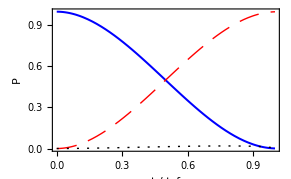

```mathematica
Plot[{sh10[t tf0],sh20[t tf0],sh20[t tf0](1-ct[t tf0]^2)},{t,0,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]}},PlotRange->{All,Full},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t / t_f",FontSize->16,Italic],Style["P",FontSize->16,Italic]}]
```

```mathematica
FindMaximum[sh20[t tf0](1-ct[t tf0]^2),{t,0.8}]
```

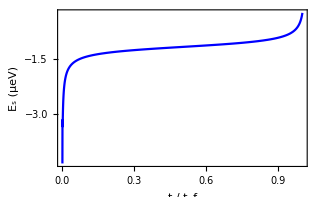

```mathematica
Plot[{fEs[t tf0]/(1.6 10^(-25))},{t,0.001,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green},{Thick,Orange},{Thick,Black,Purple}},PlotRange->{All,Full},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t / t_f",FontSize->16,Italic],Style["E_s (μeV)",FontSize->16,Italic]}]
```

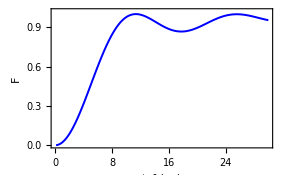

```mathematica
ListPlot[DFs,Joined->True,PlotStyle->{Thick,Blue,Thickness[0.005]},PlotRange->{All,{0,1.02}},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t_f (ns)",FontSize->16,Italic],Style["F",FontSize->16,Italic]}]
```

```mathematica
%%%%%%%%%
l: Dressaulhuas SOC 1ueV;tau:5ueV;u:3meV;
%%%%%%%%%%%%
```

```mathematica
g=1.35;muB=9.27 10^(-24);B=0.015;ET=-g muB B
```

-1.87718×10^-25

```mathematica
l=0.1 1.6 10^(-19) 10^(-6);
tau=5 1.6 10^(-19) 10^(-6);u=3000 1.6 10^(-19) 10^(-6);tf=11.5 10^(-9);hbar=1.055×10^(-34);
```

```mathematica
Est1[t_]=1/2(u+feps[t]+Sqrt[8 tau^2+(u+feps[t])^2]);Est[t_]=1/2(u+feps[t]-Sqrt[8 tau^2+(u+feps[t])^2]);
```

```mathematica
ct[t_]=-((feps[t]+u+√(8 tau^2+(u+feps[t])^2))/(√(8tau^2+(feps[t]+u+√(8tau^2+(feps[t]+u)^2))^2)));c1t[t_]=-((feps[t]+u-√(8 tau^2+(u+feps[t])^2))/(√(8tau^2+(feps[t]+u-√(8tau^2+(feps[t]+u)^2))^2)));
```

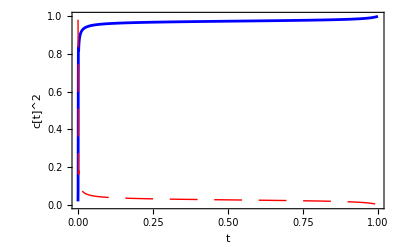

```mathematica
Plot[{ct[t tf]^2,c1t[t tf]^2},{t,0,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.01,0.025}]}},
PlotRange->{{0,1},{0,1}},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t",FontSize->20,Italic],Style["c[t]^2",FontSize->20]}]
```

```mathematica
H0[t_]={{ET, l/100,l /Sqrt[1-ct[t]^2]},{l/100,0,Sqrt[2]tau},{l/Sqrt[1-ct[t]^2],Sqrt[2]tau,u+feps[t]}};
```

```mathematica
E1[t_]=Eigenvalues[H0[t]][[1]];E2[t_]=Eigenvalues[H0[t]][[2]];
```

```mathematica
E3[t_]=Eigenvalues[H0[t]][[3]];
```

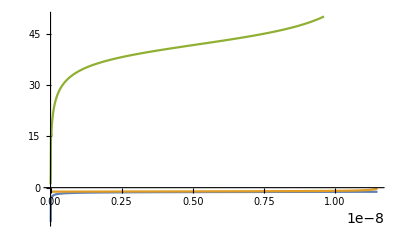

```mathematica
Plot[{E1[t]/(1.6 10^(-25)),E2[t]/(1.6 10^(-25)),E3[t]/(1.6 10^(-25))},{t,0,tf},PlotRange->{-10,50}]
```

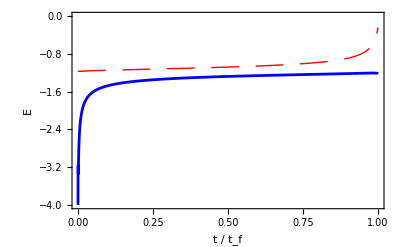

```mathematica
Plot[{E1[t tf]/(1.6 10^(-25)),E2[t tf]/(1.6 10^(-25))},{t,0.001,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green},{Thick,Orange},{Thick,Black,Purple}},PlotRange->{All,{-4,0}},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t / t_f",FontSize->16,Italic],Style["E",FontSize->16,Italic]}]
```

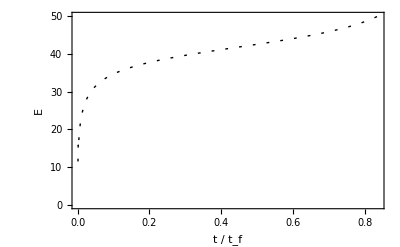

```mathematica
Plot[{E3[t tf]/(1.6 10^(-25))},{t,0.001,1},PlotStyle->{{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green},{Thick,Orange},{Thick,Black,Purple}},PlotRange->{All,{0,50}},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t / t_f",FontSize->16,Italic],Style["E",FontSize->16,Italic]}]
```

```mathematica
s3=NDSolve[{
I hbar h1'[t]==(ET h1[t]+ ( ct[t]/Sqrt[1-ct[t]^2]l/100+l) h2[t]+( c1t[t]/Sqrt[1-ct[t]^2]l/100+Sqrt[1-c1t[t]^2] l/Sqrt[1-ct[t]^2] )  h3[t]),
I hbar h2'[t]==( ( ct[t]/Sqrt[1-ct[t]^2]l/100+l)  h1[t]+fEs[t]h2[t]),
I hbar h3'[t]==(( c1t[t]/Sqrt[1-ct[t]^2]l/100+Sqrt[1-c1t[t]^2] l/Sqrt[1-ct[t]^2])  h1[t]+Est1[t] h3[t]),
h1[0]==1,h2[0]==0,h3[0]==0},{h1[t],h2[t],h3[t]},{t,0,tf},MaxSteps->∞];
sh31[t_]=Abs[h1[t]/.s3]^2;
sh32[t_]=Abs[h2[t]/.s3]^2;sh33[t_]=Abs[h3[t]/.s3]^2;
```

```mathematica
sh32[ tf] ct[tf]^2
```

{0.992374}

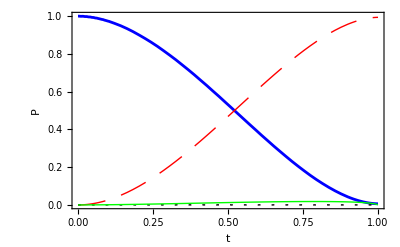

```mathematica
Plot[{sh31[t tf],sh32[t tf],sh33[t tf],sh32[t tf](1-(ct[t tf])^2)},{t,0,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green}},PlotRange->{All,Full},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t ",FontSize->16,Italic],Style["P",FontSize->16,Italic]}]
```

```mathematica
FindMaximum[sh32[t tf](1-(ct[t tf])^2),{t,0.8}]
```

{0.0181258,{t→0.785343}}

```mathematica
s32=NDSolve[{
I hbar h1'[t]==ET h1[t]+ l/Sqrt[1-ct[t]^2]/100 h2[t]+ l /Sqrt[1-ct[t]^2]h3[t],
I hbar h2'[t]== l/Sqrt[1-ct[t]^2]/100 h1[t]+Sqrt[2]tau h3[t],
I hbar h3'[t]==  l/Sqrt[1-ct[t]^2] h1[t]+Sqrt[2]tau h2[t]+(feps[t]+u) h3[t],
h1[0]==1,h2[0]==0,h3[0]==0},{h1[t],h2[t],h3[t]},{t,0,tf},MaxSteps->∞];
sh12[t_]=Abs[h1[t]/.s32]^2;
sh22[t_]=Abs[h2[t]/.s32]^2;sh32[t_]=Abs[h3[t]/.s32]^2;
```

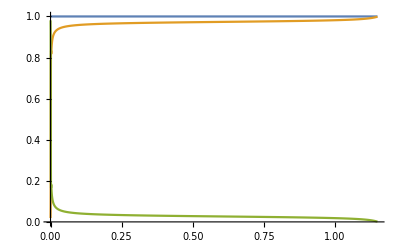

```mathematica
Plot[{c1t[t]^2+ct[t]^2,ct[t]^2,c1t[t]^2},{t,0,tf}]
```

```mathematica
sh22[tf]
```

{0.99106}

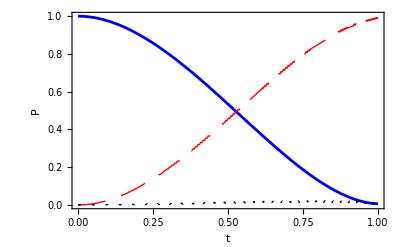

```mathematica
Plot[{sh12[t tf],sh22[t tf],sh32[t tf]},{t,0,1},PlotStyle->{{Thick,Blue,Thickness[0.005]},{Thick,Red,Dashing[{0.05,0.03}]},{Thick,Black,Dashing[{0.005,0.02}]},{Thick,Green},{Thick,Orange},{Thick,Black,Purple}},PlotRange->{All,Full},Frame->True,FrameStyle->Directive[Thickness[0.004],16],FrameLabel->{Style["t ",FontSize->16,Italic],Style["P",FontSize->16,Italic]}]
```